```mathematica
symb = Ac[r,θ]*Cos[-2*ω*t + 2*m*ϕ] + Bc[r,θ]*Sin[-2*ω*t + 2*m*ϕ] +Cc[r,θ]
FourierTransform[symb,t,ωt]/.DiracDelta->Identity//Simplify
FourierCoefficient[%,ϕ,2*m]
```

```mathematica
(-1)^(2*m) 2π FourierCoefficient[FourierTransform[symb,t,ωT]/.{DiracDelta[a_]:>1},ϕ,2*m]//Timing
```

```mathematica
FileNames[All,"/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/NilsSiemonsenCode/OG_Code_MyExecution/GWoutput/"];
dat = Import/@%;
nilsgwdat = dat[[All, 10]];

mydat = getResults[$SolutionPath, {{"m", 1}, {"n",0}}];
mydat = mydat[[Ordering[mydat[[All, "Parameters", "μNv"]]]]];
```

Plot::plln: Limiting value TeuInterEnv`Procamass in {TeuInterEnv`μin,0.05,TeuInterEnv`Procamass} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Plot::plln: Limiting value TeuInterEnv`Procamass in {TeuInterEnv`μin,0.05,TeuInterEnv`Procamass} is not a machine-sized real number.

```mathematica
mydat[[26]];
((mydat[[26]]["Derived", "Normalization", "Normalization"])^2/Sqrt[mydat[[26]]["Derived", "Normalization", "TotalEnergy"]])/2
```

0.00338786

```mathematica
enden = FKKSEnergyDensity[MySolution, ToCompiled->True];
```

```mathematica
EnDen = {r,θ,ϕ}->enden[0,r,θ,ϕ];
weight = {r,θ}|->Evaluate[Kerrmetweight[r,θ,0.9]];
```

CompiledFunction::cfsa: Argument r at position 2 should be a machine-size real number.

```mathematica
integrand[r_?NumericQ, θ_?NumericQ, ϕ_?NumericQ]:=EnDen[r,θ,ϕ]*weight[r,θ]
```

```mathematica
enden[0,2,2,2]*weight[2,2]
```

0.107108+0. ⅈ

```mathematica
<|"GWPower"->3.02888106533312959207988372279`9.64469500030789*^-9,"NormalizedGWPower"->6.5587765454950745657378474006601`9.644694999782216*^-7,"ProcaMass"->0.17015503875968990277200987180138780215`20.,"ProcaNormalizedEnergy"->0.06795719162165910432369751720166174206`10.|>
```

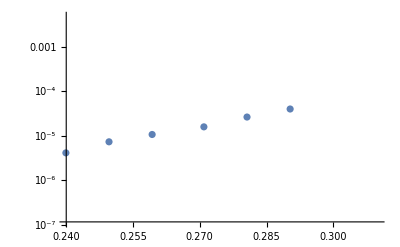

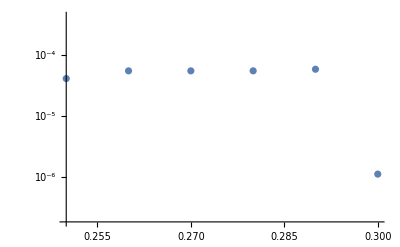

```mathematica
ListLogPlot[Thread[{gwdat[[All, "ProcaMass"]],gwdat[[All, "NormalizedGWPower"]]}],PlotRange->{{0.24,0.31}, {All, All}}]
ListLogPlot[Thread[{mydat[[All, "Parameters", "μNv"]],mydat[[All, "Derived", "Einf"]]/(1-mydat[[All, "Derived", "Normalization", "FinalMass"]])^2}], PlotRange->{{0.25,0.3}, {All, All}}]
```

```mathematica
MySolution["Solution", "ω"]//Precision
NilsSolution["Solution", "ω"]//Precision
```